```mathematica
f=y[x]/.NDSolve[{y''[x] + (1+ Sin[x]^2)y'[x]+Cos[x]^2 y[x]==3Exp[x],y[0.2]==Exp[0.2],y[1]==Exp[1.0]},y[x],x][[1]]
```

InterpolatingFunction[…][x]

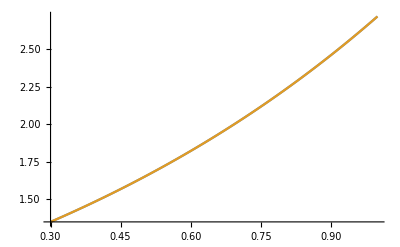

```mathematica
Plot[{f, Exp[x]},{x,0.3,1}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

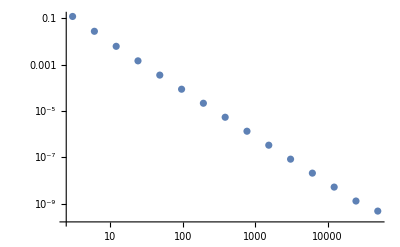

```mathematica
dat = Import["out.txt","Table"];
ListPlot[dat,ScalingFunctions->{"Log","Log"}]
```

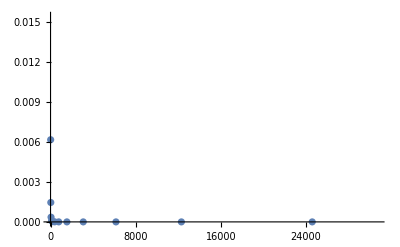

```mathematica
ListPlot[dat]
```